## use Lorenz equations to demonstrate chaos (sensitive dependence on initial conditions), Fig. 11.5

```mathematica
Clear["Global`*"];
```

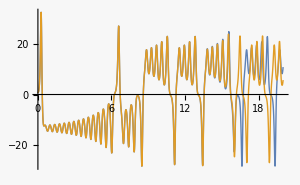

```mathematica
tend=20;σ=16; b=4;r=45.6;a=0.4;

 eq={   x'[t]==σ(y[t]-x[t]), 
        y'[t]==x[t](r-z[t])-y[t],
        z'[t]==x[t]y[t]-b z[t]               };

init1={x[0]==1,y[0]==0,z[0]==0};
{xs1,ys1,zs1}=NDSolveValue[{eq,init1},{x,y,z},{t,0,tend}];

init2={x[0]==1.0001,y[0]==0,z[0]==0};
{xs2,ys2,zs2}=NDSolveValue[{eq,init2},{x,y,z},{t,0,tend}];

p=Plot[{xs1[t],xs2[t]},{t,0,tend},ImageSize->300]
```

Export data

```mathematica
dt=0.01;
xs1t=Table[xs1[t],{t,0,tend,dt}];
xs2t=Table[xs2[t],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["lorenzChaos.dat",Flatten/@Transpose[{xs1t,xs2t}],"Table"];
*)
```